```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->NotebookDirectory[]]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,0->3],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"QCD"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"QCD"}]];
```

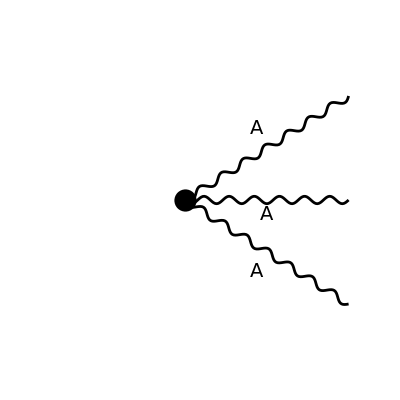

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3},LoopMomenta->{},ChangeDimension->4,List->False]
```

Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] (-g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]+g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p3]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]])

```mathematica
FCClearScalarProducts[];
(*SetMandelstam[x,{ p1 , p2, p3} ,{ 0 , 0 , 0} ];*)
```

```mathematica
amp[1]=amp[0] // Contract //SUNSimplify
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
amp[2] = amp[1] // ExpandScalarProduct
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
amp[3] =FeynAmpDenominatorExplicit[amp[2]]
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
amp[4] = amp[3]// ExpandScalarProduct  // Simplify
```

-g (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]

```mathematica
ampIso = FCColorIsolate[amp[4],Head->colorS]
```

-g colorS[SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[a3]]] (Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]])

```mathematica
FeynCalcExternal[amp[4]]
```

-g (SP[p1,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]) SUNF[a1,a2,a3]

```mathematica
diags2=InsertFields[CreateTopologies[0,0->4],{}->{V[1,{a1}],V[1,{a2}],V[1,{a3}],V[1,{a4}]},InsertionLevel->{Particles},Model->FileNameJoin[{NotebookDirectory[],"QCD"}], GenericModel ->FileNameJoin[{NotebookDirectory[],"QCD"}]];
```

```mathematica
amp2[0]=FCFAConvert[CreateFeynAmp[diags2, PreFactor->1],IncomingMomenta->{},OutgoingMomenta->{p1,p2,p3,p4},LoopMomenta->{},ChangeDimension->4,List->False]
```

-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p2+p3],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (g Pair[LorentzIndex[Lor1],Momentum[p2+p3]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor1],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor4],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor4],Momentum[-p2-p3]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor5],Momentum[p4]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]]) (g Pair[LorentzIndex[Lor2],Momentum[-p2-p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor3],Momentum[p2+p3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor6],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor6],Momentum[p3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p2+p3],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (g Pair[LorentzIndex[Lor1],Momentum[p2+p3]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor1],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor4],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor4],Momentum[-p2-p3]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor5],Momentum[p4]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]]) (g Pair[LorentzIndex[Lor2],Momentum[-p2-p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor3],Momentum[p2+p3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor6],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor6],Momentum[p3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p2+p3],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (g Pair[LorentzIndex[Lor1],Momentum[p2+p3]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor1],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor4],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor4],Momentum[-p2-p3]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor5],Momentum[p4]] SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]]) (g Pair[LorentzIndex[Lor2],Momentum[-p2-p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor3],Momentum[p2+p3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor6],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor6],Momentum[p3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p2+p4],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (-g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],Momentum[p2+p4]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor3],Momentum[-p2-p4]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor5],Momentum[p3]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]]) (g Pair[LorentzIndex[Lor2],Momentum[-p2-p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor2],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p2+p4]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor2],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p4]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p2+p4],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (-g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],Momentum[p2+p4]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor3],Momentum[-p2-p4]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor5],Momentum[p3]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]]) (g Pair[LorentzIndex[Lor2],Momentum[-p2-p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor2],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p2+p4]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor2],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p4]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p2+p4],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (-g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],Momentum[p2+p4]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor3],Momentum[-p2-p4]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor5],Momentum[p3]] SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]]) (g Pair[LorentzIndex[Lor2],Momentum[-p2-p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor2],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p2+p4]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor2],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor2],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p4]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p3+p4],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (-g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],Momentum[p3+p4]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor2],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor2],Momentum[-p3-p4]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor5],Momentum[p2]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]]) (g Pair[LorentzIndex[Lor3],Momentum[-p3-p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor3],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p3+p4]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]-g Pair[LorentzIndex[Lor3],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p4]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p3+p4],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (-g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],Momentum[p3+p4]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor2],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor2],Momentum[-p3-p4]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor5],Momentum[p2]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]]) (g Pair[LorentzIndex[Lor3],Momentum[-p3-p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor3],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p3+p4]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]]-g Pair[LorentzIndex[Lor3],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p4]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]])-ⅈ FeynAmpDenominator[PropagatorDenominator[Momentum[p3+p4],0]] Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] Pair[LorentzIndex[Lor5],LorentzIndex[Lor6]] (-g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],Momentum[p3+p4]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor5]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor2],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor5]] Pair[LorentzIndex[Lor2],Momentum[-p3-p4]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor5],Momentum[p1]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor5],Momentum[p2]] SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]]) (g Pair[LorentzIndex[Lor3],Momentum[-p3-p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor3],Momentum[p4]] Pair[LorentzIndex[Lor4],LorentzIndex[Lor6]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor6]] Pair[LorentzIndex[Lor4],Momentum[p3+p4]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]]-g Pair[LorentzIndex[Lor3],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]]+g Pair[LorentzIndex[Lor3],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor6],Momentum[p4]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]])+Pair[LorentzIndex[Lor1],Momentum[Polarization[p1,-ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] Pair[LorentzIndex[Lor4],Momentum[Polarization[p4,-ⅈ]]] (-ⅈ g^2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],LorentzIndex[Lor4]] (SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$20236]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$20236]]+SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$20235]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$20235]])+ⅈ g^2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor4]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] (SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[$AL$20232]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[$AL$20232]]+SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$20231]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$20231]])-ⅈ g^2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor4]] (-SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[$AL$20234]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[$AL$20234]]+SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[$AL$20233]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[$AL$20233]]))

```mathematica
amp2[1]=amp2[0] // Contract //SUNSimplify//FeynAmpDenominatorExplicit// ExpandScalarProduct  // Simplify//FeynCalcExternal
```

-ⅈ g^2 (((-SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]])/(SP[p2,p2]+2 SP[p2,p3]+SP[p3,p3])+((-SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]])/(SP[p2,p2]+2 SP[p2,p3]+SP[p3,p3])+((-SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p3,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]])/(SP[p2,p2]+2 SP[p2,p3]+SP[p3,p3])-(SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV[sun1151]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV[sun1151]]]+((-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]])/(SP[p2,p2]+2 SP[p2,p4]+SP[p4,p4])+((-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]])/(SP[p2,p2]+2 SP[p2,p4]+SP[p4,p4])+((-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p4,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]])/(SP[p2,p2]+2 SP[p2,p4]+SP[p4,p4])-(SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[FCGV[sun1151]]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[FCGV[sun1151]]]+((-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]])/(SP[p3,p3]+2 SP[p3,p4]+SP[p4,p4])+((-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]])/(SP[p3,p3]+2 SP[p3,p4]+SP[p4,p4])+((-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p2,Polarization[p4,-ⅈ]] (SP[p3,Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p3,-ⅈ]]) SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-SP[p1,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p3,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]])/(SP[p3,p3]+2 SP[p3,p4]+SP[p4,p4])-(SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[FCGV[sun1151]]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[FCGV[sun1151]]])

```mathematica
amp2[1] /. SP[x_,x_]->0/.SP[y_,Polarization[y_,-I]]->0
```

-ⅈ g^2 (1/(2 SP[p2,p3])(2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+1/(2 SP[p2,p3])(2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+1/(2 SP[p2,p3])(2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]-(SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV[sun1151]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV[sun1151]]]+1/(2 SP[p2,p4])(-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+1/(2 SP[p2,p4])(-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+1/(2 SP[p2,p4])(-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]-(SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[FCGV[sun1151]]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[FCGV[sun1151]]]+1/(2 SP[p3,p4])(-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+1/(2 SP[p3,p4])(-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]]+1/(2 SP[p3,p4])(-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]]-(SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[FCGV[sun1151]]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[FCGV[sun1151]]])

```mathematica
FeynCalcExternal[%]
```

-ⅈ g^2 (-((SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[a1,a4,FCGV[sun1151]] SUNF[a2,a3,FCGV[sun1151]])-(SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[a1,a3,FCGV[sun1151]] SUNF[a2,a4,FCGV[sun1151]]-(SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[a1,a2,FCGV[sun1151]] SUNF[a3,a4,FCGV[sun1151]]+1/(2 SP[p2,p3])(2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]]+1/(2 SP[p2,p3])(2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]]+1/(2 SP[p2,p3])(2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p1,Polarization[p4,-ⅈ]] (2 SP[p2,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]])-2 SP[p2,Polarization[p3,-ⅈ]] (SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]]+1/(2 SP[p2,p4])(-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]]+1/(2 SP[p2,p4])(-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]]+1/(2 SP[p2,p4])(-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p2] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,p4] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p3,-ⅈ]] (-2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])+SP[p1,Polarization[p3,-ⅈ]] (2 SP[p2,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]+SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]])-2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]]+1/(2 SP[p3,p4])(-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]]+1/(2 SP[p3,p4])(-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]]+1/(2 SP[p3,p4])(-2 SP[p1,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p2,Polarization[p3,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]-2 SP[p2,Polarization[p4,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]]+2 SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p3,-ⅈ]]-2 SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p4,Polarization[p2,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p1,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p3,Polarization[p4,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p3,Polarization[p4,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p3,-ⅈ]]+2 SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p4,Polarization[p1,-ⅈ]] SP[p4,Polarization[p3,-ⅈ]] SP[Polarization[p2,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,Polarization[p2,-ⅈ]] SP[p3,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,Polarization[p1,-ⅈ]] SP[p3,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-2 SP[p3,Polarization[p2,-ⅈ]] SP[p4,Polarization[p1,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+2 SP[p3,Polarization[p1,-ⅈ]] SP[p4,Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p1,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p1,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]-SP[p2,p3] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]+SP[p2,p4] SP[Polarization[p1,-ⅈ],Polarization[p2,-ⅈ]] SP[Polarization[p3,-ⅈ],Polarization[p4,-ⅈ]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]])

```mathematica
%//SUNSimplify
```

-((ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p2],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[1]])/(2 Pair[Momentum[p2],Momentum[p3]]))-(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p2],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[2]])/(2 Pair[Momentum[p2],Momentum[p3]])-(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p2],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+Pair[Momentum[p3],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a4],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a3],ExplicitSUNIndex[3]])/(2 Pair[Momentum[p2],Momentum[p3]])+ⅈ g^2 (Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a4],SUNIndex[FCGV[sun1401]]] SUNF[SUNIndex[a2],SUNIndex[a3],SUNIndex[FCGV[sun1401]]]-(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p3],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[1]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[1]])/(2 Pair[Momentum[p2],Momentum[p4]])-(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p3],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[2]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[2]])/(2 Pair[Momentum[p2],Momentum[p4]])-(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p3],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a3],ExplicitSUNIndex[3]] SUNF[SUNIndex[a2],SUNIndex[a4],ExplicitSUNIndex[3]])/(2 Pair[Momentum[p2],Momentum[p4]])+ⅈ g^2 (Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a3],SUNIndex[FCGV[sun1401]]] SUNF[SUNIndex[a2],SUNIndex[a4],SUNIndex[FCGV[sun1401]]]+(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[1]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[1]])/(2 Pair[Momentum[p3],Momentum[p4]])+(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[2]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[2]])/(2 Pair[Momentum[p3],Momentum[p4]])+(ⅈ g^2 (2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-2 Pair[Momentum[p3],Momentum[Polarization[p1,-ⅈ]]] Pair[Momentum[p4],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p1],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]+Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]-Pair[Momentum[p2],Momentum[p4]] Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[p3,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],ExplicitSUNIndex[3]] SUNF[SUNIndex[a3],SUNIndex[a4],ExplicitSUNIndex[3]])/(2 Pair[Momentum[p3],Momentum[p4]])+ⅈ g^2 (Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p4,-ⅈ]]]) SUNF[SUNIndex[a1],SUNIndex[a2],SUNIndex[FCGV[sun1401]]] SUNF[SUNIndex[a3],SUNIndex[a4],SUNIndex[FCGV[sun1401]]]

```mathematica
SUNTrace[%]
```